```mathematica
t=.;U=.;μ1 =.; μ2=.;
```

```mathematica
t=1;U=3;μ1 =-1; μ2=1;
```

```mathematica
H2={{μ1+μ2-U/2,0,-t,-t},{0,μ1+μ2-U/2,t,t},{-t,t,2μ1+U/2,0},{-t,t,0,2μ2+U/2}}
```

{{-3/2,0,-1,-1},{0,-3/2,1,1},{-1,1,-1/2,0},{-1,1,0,7/2}}

```mathematica
H2EigVec=N[Map[Normalize,Eigenvectors[H2]]]
```

{{-0.1935,0.1935,0.0878735,0.957807},{0.585835,-0.585835,0.527381,0.188321},{0.707107,0.707107,0.,0.},{0.345479,-0.345479,-0.845073,0.21712}}

```mathematica
H2EigVals=N[Eigenvalues[H2]]
```

{3.90405,-2.72168,-1.5,0.31763}

```mathematica
GR[t_,tp_]:=HeavisideTheta[t]*HeavisideTheta[tp]*N[-I Transpose[H2EigVec].DiagonalMatrix[Exp[-I*t* H2EigVals]].DiagonalMatrix[Exp[I*tp* H2EigVals]]. H2EigVec]

GR2[t_,tp_]:=HeavisideTheta[t]*HeavisideTheta[tp]*N[-I MatrixExp[-I*t* H2].ConjugateTranspose[MatrixExp[-I*tp* H2]]]
```

```mathematica
FT[tav_,w_]:=-1/Pi Im[NIntegrate[GR2[tav+trel/2,tav-trel/2] Exp[I w trel],{trel,0,24}]];
```

```mathematica
FTTable=Table[FT[12,w],{w,-10,10,0.1}];
```

```mathematica
wlist=Table[w,{w,-10,10,0.1}];
Length[FTTable]
```

201

```mathematica
wlist=Table[w,{w,-10,10,0.1}];
```

```mathematica
wlist=Table[w,{w,-10,10,0.1}];
```

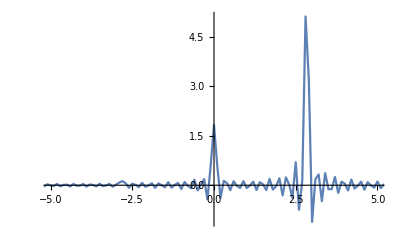

```mathematica
wlist=Table[w,{w,-10,10,0.1}];
plotlist = Transpose[{wlist,FTTable[[;;,4,4]]}];
ListPlot[plotlist,Joined->True, PlotRange->{{-5,5},Full}]
```

```mathematica
a5=OpenWrite["calc6.dat",FormatType->OutputForm];
Table[Table[Table[Write[a5,ToString[DecimalForm[FTTable[[w,i,j]],{∞,9}]]],{j,1,4}],{i,1,4}],{w,1,201}];
Close[a5];
```

```mathematica
t=.;U=.
```

```mathematica
c=Array[0,{4,16,16}];
cdag=Array[0,{4,16,16}];
Table[c[[i+1,;;,;;]]=ArrayReshape[ReadList["~/Libraries/hybfermion/build/c_"<>ToString[i]<>".dat",Number],{16,16}],{i,0,3}];
Table[cdag[[i+1,;;,;;]]=ArrayReshape[ReadList["~/Libraries/hybfermion/build/cdag_"<>ToString[i]<>".dat",Number],{16,16}],{i,0,3}];
IM=IdentityMatrix[16];
```

```mathematica
t=1;U=1;μ=0;ϵ0=-1;ϵ1=1;β=20;
H=-t(cdag[[1]].c[[3]]+cdag[[3]].c[[1]]+cdag[[2]].c[[4]]+cdag[[4]].c[[2]]) +U((cdag[[1]].c[[1]]-1/2 IM).(cdag[[2]].c[[2]]-1/2 IM)+(cdag[[3]].c[[3]]-1/2 IM).(cdag[[4]].c[[4]]-1/2 IM))-μ(cdag[[1]].c[[1]]+cdag[[2]].c[[2]]+cdag[[3]].c[[3]]+cdag[[4]].c[[4]])+ϵ0 cdag[[1]].c[[1]]+ϵ0 cdag[[2]].c[[2]]+ϵ1 cdag[[3]].c[[3]]+ϵ1 cdag[[4]].c[[4]];
Z=N[Tr[MatrixExp[-β H]]];
HEigVals = Eigenvalues[H];
HEigVecs = Map[Normalize,Eigenvectors[H]];
N[HEigVecs.Transpose[HEigVecs]]
```

{{1.,1.11022×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.11022×10^-16,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.55112×10^-17},{0.,0.,1.,0.,0.,0.,-5.55112×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,-5.55112×10^-17,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,-5.55112×10^-17,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,-5.55112×10^-17,0.,0.,0.,0.,0.,0.},{0.,0.,-5.55112×10^-17,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-5.55112×10^-17,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-5.55112×10^-17,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-5.55112×10^-17,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,5.55112×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}}

```mathematica
ReadFile=OpenRead["~/Libraries/NEdyson/build/programs/Gfree_GM.dat"];
Table[Read[ReadFile,Number],{i,1,6}];
GMFreeMyCode=Table[Table[Read[ReadFile,Number],{t,1,8}],{t,1,601}];
```

```mathematica
GM=-Table[Table[Table[1/Z Tr[MatrixExp[(-β+τ)H].c[[i]].MatrixExp[-τ H].cdag[[j]]],{τ,0,β,β/100}],{i,1,4}],{j,1,4}];
```

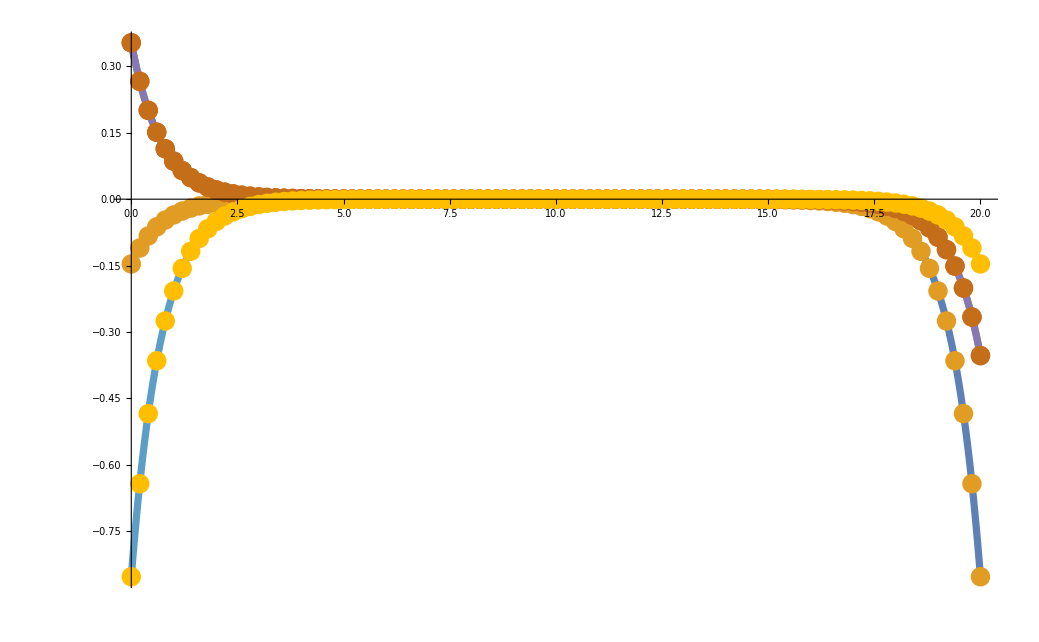

```mathematica
ListPlot[{Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,1]]}],Transpose[{Range[0,β,β/100],GM[[1,1,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,3]]}],Transpose[{Range[0,β,β/100],GM[[1,3,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,5]]}],Transpose[{Range[0,β,β/100],GM[[3,1,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,7]]}],Transpose[{Range[0,β,β/100],GM[[3,3,;;]]}]},PlotRange->Full,Joined->{True, False,True, False,True, False,True, False},PlotStyle->{Thickness[0.005]},PlotMarkers->{None,Style[•,20],None,Style[•,20],None,Style[•,20],None,Style[•,20]}]
```

```mathematica
GMInteract=-Table[Table[Table[1/Z Tr[MatrixExp[(-β+τ)H].c[[i]].MatrixExp[-τ H].cdag[[j]]],{τ,0,β,β/100}],{i,1,4}],{j,1,4}];
```

$Aborted

```mathematica
ReadFile=OpenRead["~/Libraries/NEdysondata/noquench/N2U1B20/Ntau600Nt1600/G_GM.dat"];
Table[Read[ReadFile,Number],{i,1,6}];
GMFreeMyCode=Table[Table[Read[ReadFile,Number],{t,1,8}],{t,1,601}];
```

```mathematica
ListPlot[{Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,1]]}],Transpose[{Range[0,β,β/100],GMInteract[[1,1,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,3]]}],Transpose[{Range[0,β,β/100],GMInteract[[1,3,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,5]]}],Transpose[{Range[0,β,β/100],GMInteract[[3,1,;;]]}],Transpose[{Range[0,β+1/600,β/600],GMFreeMyCode[[;;,7]]}],Transpose[{Range[0,β,β/100],GMInteract[[3,3,;;]]}],Transpose[{Range[0,β,β/100],GM[[1,1,;;]]}],Transpose[{Range[0,β,β/100],GM[[1,3,;;]]}],Transpose[{Range[0,β,β/100],GM[[3,1,;;]]}],Transpose[{Range[0,β,β/100],GM[[3,3,;;]]}]},PlotRange->Full,Joined->{True, False,True, False,True, False,True, False, False,False,False,False},PlotStyle->{Thickness[0.005]},PlotMarkers->{None,Style[•,20],None,Style[•,20],None,Style[•,20],None,Style[•,20],Style[☺,20],Style[☺,20],Style[☺,20],Style[☺,20]}]
```

-Graphics-

```mathematica
ReadFile=OpenRead["~/Libraries/NEdyson/build/programs/Gfree_GM.dat"];
Table[Read[ReadFile,Number],{i,1,6}];
GMFreeMyCode=Table[Table[Read[ReadFile,Number],{t,1,8}],{t,1,601}];
```

```mathematica
GRInt=-Table[Table[Table[1/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β-I t)HEigVals]].HEigVecs.c[[i]].Transpose[HEigVecs].DiagonalMatrix[Exp[(-I t)HEigVals]].HEigVecs.cdag[[j]]],{t,0,24,24/1000}],{i,1,4,2}],{j,1,4,2}];
```

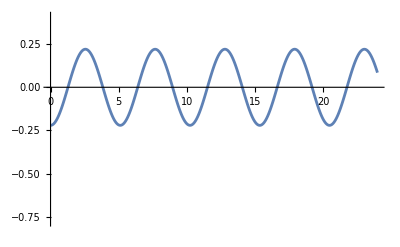

```mathematica
ListPlot[{Transpose[{Range[0,24,24/1000],Re[GRInt[[1,1,;;]]]}],Transpose[{Range[0,24,24/1000],GRInt[[1,2,;;]]}],Transpose[{Range[0,24,24/1000],GRInt[[2,1,;;]]}],Transpose[{Range[0,24,24/1000],GRInt[[2,2,;;]]}]},PlotRange->Full,Joined->{True,True,True,True},PlotStyle->{Thickness[0.005]},PlotMarkers->{None,None,None,None}]
```

```mathematica
GL=Table[Table[Table[I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β+I t)HEigVals]].HEigVecs.cdag[[j]].Transpose[HEigVecs].DiagonalMatrix[Exp[(I t)HEigVals]].HEigVecs.c[[i]]],{t,0,24,24/200}],{i,1,4,2}],{j,1,4,2}];
GG = Table[Table[Table[-I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β-I t)HEigVals]].HEigVecs.c[[i]].Transpose[HEigVecs].DiagonalMatrix[Exp[-I t HEigVals]].HEigVecs.cdag[[j]]],{t,0,24,24/200}],{i,1,4,2}],{j,1,4,2}];
GR = GG-GL;
```

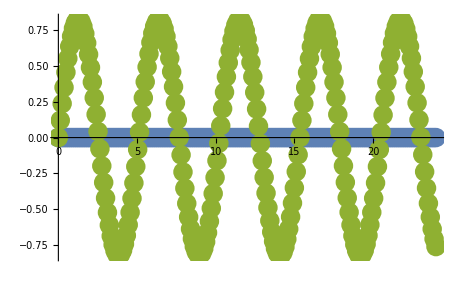

```mathematica
ListPlot[{Transpose[{Range[0,24,24/200],Im[GR[[2,1,;;]]]}],Transpose[{Range[0,24+1/1600,24/1600],GRMyCode[[;;,6]]}],Transpose[{Range[0,24,24/200],Re[GR[[2,1,;;]]]}],Transpose[{Range[0,24+1/1600,24/1600],GRMyCode[[;;,5]]}]},PlotRange->Full,Joined->{False,True},PlotStyle->{Thickness[0.005]},PlotMarkers->{Style[•,20],None}]
```

```mathematica
ReadFile=OpenRead["~/Libraries/NEdyson/python/plot/GRdata"];
GRMyCode=Table[Table[Read[ReadFile,Number],{i,1,8}],{t,1,1601}];
```

```mathematica
Length[GMFreeMyCode]
```

1601

```mathematica
GLf[t_,tp_,i_,j_]:=I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β+I t-I tp)HEigVals]].HEigVecs.cdag[[j]].Transpose[HEigVecs].DiagonalMatrix[Exp[(I t-I tp)HEigVals]].HEigVecs.c[[i]]];
GGf[t_,tp_,i_,j_]:=-I/Z Tr[Transpose[HEigVecs].DiagonalMatrix[Exp[-(β-I t+I tp)HEigVals]].HEigVecs.c[[i]].Transpose[HEigVecs].DiagonalMatrix[Exp[(-I t +I tp)HEigVals]].HEigVecs.cdag[[j]]];
GRf[t_,tp_,i_,j_]:= GGf[t,tp,i,j]-GLf[t,tp,i,j];
```

```mathematica
FTf[tav_,w_,i_,j_]:=-1/Pi Im[NIntegrate[GRf[tav+trel/2,tav-trel/2,i,j]Exp[I w trel],{trel,0,24}]];
```

```mathematica
FTfTable=Table[FTf[12,w,1,1],{w,-10,10,0.1}];
wlist=Table[w,{w,-10,10,0.1}];
plotlist = Transpose[{wlist,FTfTable[[;;]]}];
```

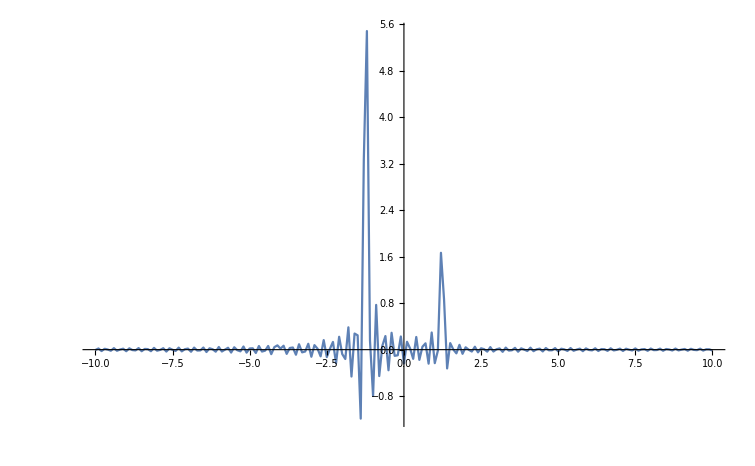

```mathematica
ListPlot[plotlist,Joined->True,PlotRange->Full]
```

```mathematica
a6=OpenWrite["calc8.dat",FormatType->OutputForm];
Table[Write[a6,ToString[DecimalForm[FTfTable[[w]],{∞,9}]]],{w,1,201}];
Close[a6];
```